```mathematica
{2021,1,14,17,5,35.603957`8.304073247467505}
{2020,8,19,21,32,56.570768`8.505167048611666}
{2020,6,30,15,15,55}
Date[]
```

{2021,1,14,17,5,35.603957}

{2020,8,19,21,32,56.570768}

{2020,6,30,15,15,55}

{2021,1,14,21,1,43.069577}

```mathematica
N[MachinePrecision,100]
```

15.95458977019100334632816142039813041871406371749175268945265543973673403154449900280714436226386712

```mathematica
nmax=500;
```

```mathematica
%%%In the formula given in Zerrili-+-equation.nb, change (i om) --> om and om**2--> om.
%%% This follow the change of ome original to (i*om)
```

```mathematica
λ0[xi_,ω_]:=-((12 (-1+xi) xi (-2+xi (6+(-4+xi) xi)))/(6+(-4+xi) xi)-(3+xi (2+xi (-27+16 xi))) ω)/(2 (-1+xi)^2 xi^2);
s0[xi_,ω_]:=-((xi^4 (-773504+793208 ω-1122911 ω^2)+16 xi^14 (25-20 ω+16 ω^2)-324 (56+167 ω^2)-432 xi (-100-167 ω+263 ω^2)-16 xi^13 (400-331 ω+278 ω^2)+xi^12 (48000-41064 ω+36185 ω^2)+6 xi^3 (82016-53164 ω+36191 ω^2)+9 xi^2 (-17424-9488 ω+36641 ω^2)-2 xi^11 (110176-97468 ω+89925 ω^2)-16 xi^7 (129896-131273 ω+129451 ω^2)+4 xi^5 (76256-91988 ω+215631 ω^2)-4 xi^9 (365520-346348 ω+344805 ω^2)+xi^10 (680528-622896 ω+599277 ω^2)+xi^6 (974256-988064 ω+715454 ω^2)+xi^8 (2168672-2126672 ω+2155398 ω^2))/(16 (-1+xi)^2 xi^2 (6-4 xi+xi^2)^2 (-3-2 xi+6 xi^2-4 xi^3+xi^4)^2))
```

```mathematica
FF0:=Series[λ0[xi,ω],{xi,1/2,nmax}]
GG0:=Series[s0[xi,ω],{xi,1/2,nmax}]
```

Array[CC, {nmax + 1, nmax + 1}];
Array[DD, {nmax + 1, nmax + 1}];

```mathematica
For[i=1,i<(nmax+2), i++,
CC[i,1]=Coefficient[FF0,(xi-1/2),(i-1)];
DD[i,1]=Coefficient[GG0,(xi-1/2),(i-1)]]
```

```mathematica
For[i=1,i<(nmax+2), i++,
CC[i,1]=Simplify[CC[i,1]];
DD[i,1]=Simplify[DD[i,1]]]
```

```mathematica
For[n=2,n<nmax+2,n++,
Print[n];
For[i=1,i<nmax+3-n,i++,
sumx=0;
sumy=0;
For[k=1,k<i+1,k++,
sumx=sumx+CC[k,1] CC[i-k+1,n-1];
sumy=sumy+DD[k,1] CC[i-k+1,n-1]
];
CC[i,n]=Expand[(i) CC[i+1,n-1]+DD[i,n-1]+sumx];
DD[i,n]=Expand[(i) DD[i+1,n-1]+sumy]
]]
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

486

487

488

489

490

491

492

493

494

495

496

497

498

499

500

501

%%%%   Solo los coeficientes de orden cero  de la serie de Taylor de λn, y sn   %%%%%%

```mathematica
c0[n_]:=Expand[CC[1,n]]
d0[n_]:=Expand[DD[1,n]]
```

```mathematica
δ[n_,ω_]:=d0[n]c0[n-1]-d0[n-1]c0[n]
```

```mathematica
raices[n_]:=N[Roots[δ[n,ω]==0,ω]]
```

%%%%    %%%%

```mathematica
R500=raices[500]
```

ω==0.00640153||ω==0.00919698||ω==0.0126686||ω==0.0197683||ω==0.0205167||ω==0.0299926||ω==0.0335727||ω==0.0411149||ω==0.0506732||ω==0.0538941||ω==0.0683368||ω==0.0711132||ω==0.0844618||ω==0.0949271||ω==0.102279||ω==0.121765||ω==0.122211||ω==0.143053||ω==0.152913||ω==0.166056||ω==0.18721||ω==0.19084||ω==0.217398||ω==0.225186||ω==0.245809||ω==0.26688||ω==0.276085||ω==0.30823||ω==0.312445||ω==0.342353||ω==0.36189||ω==0.378447||ω==0.41523||ω==0.416675||ω==0.456723||ω==0.472849||ω==0.499042||ω==0.534276||ω==0.543587||ω==0.590058||ω==0.59978||ω==0.639102||ω==0.668195||ω==0.690398||ω==0.739442||ω==0.743778||ω==0.800413||ω==0.811644||ω==0.858747||ω==0.885802||ω==0.919555||ω==0.963165||ω==0.982921||ω==1.04697||ω==1.05059||ω==1.1169||ω==1.14526||ω==1.18798||ω==1.2446||ω==1.26213||ω==1.33572||ω==1.3558||ω==1.41513||ω==1.47049||ω==1.49705||ω==1.57741||ω==1.59467||ω==1.66568||ω==1.72282||ω==1.75568||ω==1.8442||ω==1.861||ω==1.94105||ω==2.00254||ω==2.03924||ω==2.13787||ω==2.1559||ω==2.24237||ω==2.31206||ω==2.34893||ω==2.45816||ω==2.48128||ω==2.57089||ω==2.65647||ω==2.68671||ω==2.8063||ω==2.8385||ω==2.92852||ω==3.03407||ω==3.0528||ω==3.18368||ω==3.23726||ω==3.31593||ω==3.44221||ω==3.46101||ω==3.59273||ω==3.66864||ω==3.74124||ω==3.88279||ω==3.90373||ω==4.0408||ω==4.14275||ω==4.19593||ω==4.35769||ω==4.39879||ω==4.51914||ω==4.66577||ω==4.69419||ω==4.86064||ω==4.94638||ω==5.04449||ω==5.22889||ω==5.23484||ω==5.41182||ω==5.55289||ω==5.60061||ω==5.79516||ω==5.87575||ω==6.00745||ω==6.42505||ω==6.57418||ω==6.64317||ω==6.86278||ω==6.94385||ω==7.10367||ω==7.57465||ω==7.74592||ω==7.84046||ω==8.09239||ω==8.20041||ω==8.34523||ω==8.60218||ω==8.66643||ω==8.90193||ω==9.15203||ω==9.20384||ω==9.4874||ω==9.67178||ω==9.77078||ω==10.0792||ω==10.2171||ω==10.4176||ω==10.7235||ω==10.8443||ω==11.0972||ω==11.4174||ω==11.5045||ω==11.8137||ω==12.1428||ω==12.2086||ω==12.5741||ω==12.8792||ω==12.9975||ω==13.3751||ω==13.6522||ω==13.8324||ω==14.2072||ω==14.4683||ω==14.6783||ω==15.1445||ω==16.1563||ω==16.4537||ω==16.6743||ω==17.3145||ω==17.6677||ω==17.8864||ω==18.5248||ω==18.9308||ω==19.1524||ω==19.8316||ω==20.2369||ω==20.4001||ω==20.6327||ω==20.8758||ω==21.1589||ω==21.9143||ω==22.214||ω==22.3439||ω==22.6557||ω==22.9014||ω==23.1824||ω==23.3549||ω==23.6592||ω==23.9503||ω==24.0788||ω==24.4387||ω==24.6467||ω==24.8711||ω==25.1791||ω==25.3821||ω==25.6472||ω==25.9002||ω==26.1546||ω==26.3817||ω==26.6615||ω==26.8947||ω==27.1321||ω==27.4271||ω==27.6139||ω==27.917||ω==28.1408||ω==28.3839||ω==28.6721||ω==28.8657||ω==29.1701||ω==29.3794||ω==29.6476||ω==29.9041||ω==30.1281||ω==30.4156||ω==30.6241||ω==30.9099||ω==31.1345||ω==31.3963||ω==31.6485||ω==31.884||ω==32.1574||ω==32.3783||ω==32.6584||ω==32.88||ω==33.1531||ω==33.3866||ω==33.6452||ω==33.8943||ω==34.1379||ω==34.4||ω==34.6333||ω==34.9024||ω==35.132||ω==35.4016||ω==35.6335||ω==35.8988||ω==36.1363||ω==36.3956||ω==36.6388||ω==36.8931||ω==37.1403||ω==37.392||ω==37.6404||ω==37.8921||ω==38.1394||ω==38.393||ω==38.638||ω==38.8939||ω==39.1368||ω==39.3944||ω==39.6363||ω==39.8941||ω==40.1367||ω==40.393||ω==40.6379||ω==40.8912||ω==41.1395||ω==41.3892||ω==41.6411||ω==41.8876||ω==42.142||ω==42.3867||ω==42.6421||ω==42.8868||ω==43.1412||ω==43.3877||ω==43.6398||ω==43.8888||ω==44.1386||ω==44.3894||ω==44.6382||ω==44.8891||ω==45.1386||ω==45.3882||ω==45.6392||ω==45.8875||ω==46.1392||ω==46.3877||ω==46.6382||ω==46.8888||ω==47.1368||ω==47.3897||ω==47.6362||ω==47.8894||ω==48.1368||ω==48.3882||ω==48.6378||ω==48.8873||ω==49.1378||ω==49.3876||ω==49.6369||ω==49.8883||ω==50.1365||ω==50.3879||ω==50.6371||ω==50.8868||ω==51.1378||ω==51.3864||ω==51.6374||ω==51.887||ω==52.1366||ω==52.3871||ω==52.6369||ω==52.8863||ω==53.1375||ω==53.3859||ω==53.6371||ω==53.8865||ω==54.1364||ω==54.3865||ω==54.6367||ω==54.8858||ω==55.137||ω==55.3858||ω==55.6363||ω==55.8863||ω==56.1361||ω==56.3858||ω==56.6365||ω==56.8855||ω==57.1362||ω==57.3859||ω==57.6357||ω==57.8858||ω==58.1361||ω==58.3853||ω==58.6359||ω==58.8856||ω==59.1355||ω==59.3856||ω==59.6357||ω==59.8851||ω==60.1356||ω==60.3854||ω==60.6352||ω==60.8853||ω==61.1355||ω==61.385||ω==61.6353||ω==61.8852||ω==62.1351||ω==62.3849||ω==62.6353||ω==62.8848||ω==63.135||ω==63.385||ω==63.635||ω==63.8846||ω==64.135||ω==64.3848||ω==64.6347||ω==64.8847||ω==65.1349||ω==65.3844||ω==65.6347||ω==65.8846||ω==66.1344||ω==66.3848||ω==66.6337||ω==66.8853||ω==67.1349||ω==67.3804||ω==67.6436||ω==67.8727||ω==68.1371||ω==68.4167||ω==68.5655||ω==69.3075||ω==70.2596||ω==71.2753||ω==72.2493||ω==73.2004||ω==74.1282||ω==75.0344||ω==75.9277||ω==76.7103||ω==0.0785661-0.410396 ⅈ||ω==0.0785661+0.410396 ⅈ||ω==0.238529-0.380674 ⅈ||ω==0.238529+0.380674 ⅈ||ω==0.408204-0.322741 ⅈ||ω==0.408204+0.322741 ⅈ||ω==0.598369-0.24593 ⅈ||ω==0.598369+0.24593 ⅈ||ω==0.826413-0.17366 ⅈ||ω==0.826413+0.17366 ⅈ||ω==1.09376-0.142384 ⅈ||ω==1.09376+0.142384 ⅈ||ω==1.35813-0.141191 ⅈ||ω==1.35813+0.141191 ⅈ||ω==1.61709-0.144575 ⅈ||ω==1.61709+0.144575 ⅈ||ω==1.87358-0.148357 ⅈ||ω==1.87358+0.148357 ⅈ||ω==2.12844-0.151971 ⅈ||ω==2.12844+0.151971 ⅈ||ω==2.38243-0.15548 ⅈ||ω==2.38243+0.15548 ⅈ||ω==2.63541-0.158314 ⅈ||ω==2.63541+0.158314 ⅈ||ω==2.88821-0.16129 ⅈ||ω==2.88821+0.16129 ⅈ||ω==3.13998-0.164095 ⅈ||ω==3.13998+0.164095 ⅈ||ω==3.39144-0.16626 ⅈ||ω==3.39144+0.16626 ⅈ||ω==3.64296-0.168193 ⅈ||ω==3.64296+0.168193 ⅈ||ω==3.89432-0.170045 ⅈ||ω==3.89432+0.170045 ⅈ||ω==4.14534-0.17184 ⅈ||ω==4.14534+0.17184 ⅈ||ω==4.39606-0.173466 ⅈ||ω==4.39606+0.173466 ⅈ||ω==4.64628-0.175284 ⅈ||ω==4.64628+0.175284 ⅈ||ω==4.89684-0.17708 ⅈ||ω==4.89684+0.17708 ⅈ||ω==5.14683-0.17906 ⅈ||ω==5.14683+0.17906 ⅈ||ω==5.3979-0.181388 ⅈ||ω==5.3979+0.181388 ⅈ||ω==5.64971-0.181854 ⅈ||ω==5.64971+0.181854 ⅈ||ω==5.89915-0.182278 ⅈ||ω==5.89915+0.182278 ⅈ||ω==6.14771-0.183082 ⅈ||ω==6.14771+0.183082 ⅈ||ω==6.21076-0.00701798 ⅈ||ω==6.21076+0.00701798 ⅈ||ω==6.3986-0.186976 ⅈ||ω==6.3986+0.186976 ⅈ||ω==6.65063-0.185261 ⅈ||ω==6.65063+0.185261 ⅈ||ω==6.89899-0.186103 ⅈ||ω==6.89899+0.186103 ⅈ||ω==7.14846-0.190422 ⅈ||ω==7.14846+0.190422 ⅈ||ω==7.33899-0.0187934 ⅈ||ω==7.33899+0.0187934 ⅈ||ω==7.40167-0.187011 ⅈ||ω==7.40167+0.187011 ⅈ||ω==7.64853-0.190718 ⅈ||ω==7.64853+0.190718 ⅈ||ω==7.90062-0.193358 ⅈ||ω==7.90062+0.193358 ⅈ||ω==8.14657-0.188382 ⅈ||ω==8.14657+0.188382 ⅈ||ω==8.40161-0.193791 ⅈ||ω==8.40161+0.193791 ⅈ||ω==8.6511-0.191232 ⅈ||ω==8.6511+0.191232 ⅈ||ω==8.89839-0.198659 ⅈ||ω==8.89839+0.198659 ⅈ||ω==9.14514-0.191201 ⅈ||ω==9.14514+0.191201 ⅈ||ω==9.3968-0.196455 ⅈ||ω==9.3968+0.196455 ⅈ||ω==9.64874-0.18851 ⅈ||ω==9.64874+0.18851 ⅈ||ω==9.90415-0.199813 ⅈ||ω==9.90415+0.199813 ⅈ||ω==10.1503-0.196102 ⅈ||ω==10.1503+0.196102 ⅈ||ω==10.4035-0.203371 ⅈ||ω==10.4035+0.203371 ⅈ||ω==10.6434-0.205083 ⅈ||ω==10.6434+0.205083 ⅈ||ω==10.8983-0.202016 ⅈ||ω==10.8983+0.202016 ⅈ||ω==11.1429-0.20743 ⅈ||ω==11.1429+0.20743 ⅈ||ω==11.3855-0.198938 ⅈ||ω==11.3855+0.198938 ⅈ||ω==11.6435-0.203754 ⅈ||ω==11.6435+0.203754 ⅈ||ω==11.8848-0.205091 ⅈ||ω==11.8848+0.205091 ⅈ||ω==12.1327-0.192871 ⅈ||ω==12.1327+0.192871 ⅈ||ω==12.3893-0.205633 ⅈ||ω==12.3893+0.205633 ⅈ||ω==12.6293-0.205873 ⅈ||ω==12.6293+0.205873 ⅈ||ω==12.879-0.197804 ⅈ||ω==12.879+0.197804 ⅈ||ω==13.1374-0.212209 ⅈ||ω==13.1374+0.212209 ⅈ||ω==13.3791-0.215758 ⅈ||ω==13.3791+0.215758 ⅈ||ω==13.6324-0.213181 ⅈ||ω==13.6324+0.213181 ⅈ||ω==13.8953-0.22235 ⅈ||ω==13.8953+0.22235 ⅈ||ω==14.1432-0.227502 ⅈ||ω==14.1432+0.227502 ⅈ||ω==14.4024-0.221126 ⅈ||ω==14.4024+0.221126 ⅈ||ω==14.6712-0.22034 ⅈ||ω==14.6712+0.22034 ⅈ||ω==14.9231-0.218506 ⅈ||ω==14.9231+0.218506 ⅈ||ω==15.1699-0.170204 ⅈ||ω==15.1699+0.170204 ⅈ||ω==15.3483-0.128301 ⅈ||ω==15.3483+0.128301 ⅈ||ω==15.5748-0.166489 ⅈ||ω==15.5748+0.166489 ⅈ||ω==15.6565-0.0303099 ⅈ||ω==15.6565+0.0303099 ⅈ||ω==15.8653-0.224256 ⅈ||ω==15.8653+0.224256 ⅈ||ω==16.1246-0.242009 ⅈ||ω==16.1246+0.242009 ⅈ||ω==16.3989-0.241555 ⅈ||ω==16.3989+0.241555 ⅈ||ω==16.6857-0.237946 ⅈ||ω==16.6857+0.237946 ⅈ||ω==16.9597-0.213226 ⅈ||ω==16.9597+0.213226 ⅈ||ω==17.0937-0.150094 ⅈ||ω==17.0937+0.150094 ⅈ||ω==17.3298-0.235277 ⅈ||ω==17.3298+0.235277 ⅈ||ω==17.6164-0.254916 ⅈ||ω==17.6164+0.254916 ⅈ||ω==17.9146-0.26075 ⅈ||ω==17.9146+0.26075 ⅈ||ω==18.209-0.249289 ⅈ||ω==18.209+0.249289 ⅈ||ω==18.3519-0.0591833 ⅈ||ω==18.3519+0.0591833 ⅈ||ω==18.5621-0.250827 ⅈ||ω==18.5621+0.250827 ⅈ||ω==18.8665-0.274376 ⅈ||ω==18.8665+0.274376 ⅈ||ω==19.1798-0.276246 ⅈ||ω==19.1798+0.276246 ⅈ||ω==19.5042-0.266042 ⅈ||ω==19.5042+0.266042 ⅈ||ω==19.5495-0.0407821 ⅈ||ω==19.5495+0.0407821 ⅈ||ω==19.8473-0.286187 ⅈ||ω==19.8473+0.286187 ⅈ||ω==20.163-0.294296 ⅈ||ω==20.163+0.294296 ⅈ||ω==20.5038-0.290412 ⅈ||ω==20.5038+0.290412 ⅈ||ω==20.846-0.30293 ⅈ||ω==20.846+0.30293 ⅈ||ω==21.1809-0.311388 ⅈ||ω==21.1809+0.311388 ⅈ||ω==21.5198-0.0533572 ⅈ||ω==21.5198+0.0533572 ⅈ||ω==21.5301-0.308737 ⅈ||ω==21.5301+0.308737 ⅈ||ω==21.8776-0.325267 ⅈ||ω==21.8776+0.325267 ⅈ||ω==22.2269-0.325367 ⅈ||ω==22.2269+0.325367 ⅈ||ω==22.5858-0.335922 ⅈ||ω==22.5858+0.335922 ⅈ||ω==22.9421-0.342508 ⅈ||ω==22.9421+0.342508 ⅈ||ω==23.3069-0.347568 ⅈ||ω==23.3069+0.347568 ⅈ||ω==23.6709-0.357617 ⅈ||ω==23.6709+0.357617 ⅈ||ω==24.0425-0.36187 ⅈ||ω==24.0425+0.36187 ⅈ||ω==24.4136-0.371855 ⅈ||ω==24.4136+0.371855 ⅈ||ω==24.7926-0.377966 ⅈ||ω==24.7926+0.377966 ⅈ||ω==25.1717-0.38639 ⅈ||ω==25.1717+0.38639 ⅈ||ω==25.5573-0.394027 ⅈ||ω==25.5573+0.394027 ⅈ||ω==25.9449-0.40208 ⅈ||ω==25.9449+0.40208 ⅈ||ω==26.3375-0.41006 ⅈ||ω==26.3375+0.41006 ⅈ||ω==26.7327-0.418234 ⅈ||ω==26.7327+0.418234 ⅈ||ω==27.133-0.426996 ⅈ||ω==27.133+0.426996 ⅈ||ω==27.5365-0.434922 ⅈ||ω==27.5365+0.434922 ⅈ||ω==27.9438-0.444027 ⅈ||ω==27.9438+0.444027 ⅈ||ω==28.3558-0.452923 ⅈ||ω==28.3558+0.452923 ⅈ||ω==28.7713-0.461563 ⅈ||ω==28.7713+0.461563 ⅈ||ω==29.1908-0.470934 ⅈ||ω==29.1908+0.470934 ⅈ||ω==29.6148-0.480365 ⅈ||ω==29.6148+0.480365 ⅈ||ω==30.0428-0.489674 ⅈ||ω==30.0428+0.489674 ⅈ||ω==30.4749-0.499304 ⅈ||ω==30.4749+0.499304 ⅈ||ω==30.9113-0.509234 ⅈ||ω==30.9113+0.509234 ⅈ||ω==31.352-0.51925 ⅈ||ω==31.352+0.51925 ⅈ||ω==31.7971-0.529374 ⅈ||ω==31.7971+0.529374 ⅈ||ω==32.2464-0.539715 ⅈ||ω==32.2464+0.539715 ⅈ||ω==32.7003-0.550293 ⅈ||ω==32.7003+0.550293 ⅈ||ω==33.1586-0.561067 ⅈ||ω==33.1586+0.561067 ⅈ||ω==33.6214-0.572017 ⅈ||ω==33.6214+0.572017 ⅈ||ω==34.0889-0.583152 ⅈ||ω==34.0889+0.583152 ⅈ||ω==34.561-0.594495 ⅈ||ω==34.561+0.594495 ⅈ||ω==35.0377-0.606056 ⅈ||ω==35.0377+0.606056 ⅈ||ω==35.5193-0.617839 ⅈ||ω==35.5193+0.617839 ⅈ||ω==36.0056-0.629845 ⅈ||ω==36.0056+0.629845 ⅈ||ω==36.4968-0.642077 ⅈ||ω==36.4968+0.642077 ⅈ||ω==36.993-0.654538 ⅈ||ω==36.993+0.654538 ⅈ||ω==37.4942-0.667235 ⅈ||ω==37.4942+0.667235 ⅈ||ω==38.0004-0.680175 ⅈ||ω==38.0004+0.680175 ⅈ||ω==38.5118-0.693364 ⅈ||ω==38.5118+0.693364 ⅈ||ω==39.0284-0.706809 ⅈ||ω==39.0284+0.706809 ⅈ||ω==39.5502-0.720516 ⅈ||ω==39.5502+0.720516 ⅈ||ω==40.0775-0.734492 ⅈ||ω==40.0775+0.734492 ⅈ||ω==40.6102-0.748743 ⅈ||ω==40.6102+0.748743 ⅈ||ω==41.1484-0.763277 ⅈ||ω==41.1484+0.763277 ⅈ||ω==41.6922-0.7781 ⅈ||ω==41.6922+0.7781 ⅈ||ω==42.2417-0.793221 ⅈ||ω==42.2417+0.793221 ⅈ||ω==42.797-0.808649 ⅈ||ω==42.797+0.808649 ⅈ||ω==43.3581-0.82439 ⅈ||ω==43.3581+0.82439 ⅈ||ω==43.9252-0.840454 ⅈ||ω==43.9252+0.840454 ⅈ||ω==44.4984-0.85685 ⅈ||ω==44.4984+0.85685 ⅈ||ω==45.0778-0.873587 ⅈ||ω==45.0778+0.873587 ⅈ||ω==45.6634-0.890675 ⅈ||ω==45.6634+0.890675 ⅈ||ω==46.2554-0.908125 ⅈ||ω==46.2554+0.908125 ⅈ||ω==46.854-0.925946 ⅈ||ω==46.854+0.925946 ⅈ||ω==47.4591-0.944151 ⅈ||ω==47.4591+0.944151 ⅈ||ω==48.071-0.962751 ⅈ||ω==48.071+0.962751 ⅈ||ω==48.6897-0.981757 ⅈ||ω==48.6897+0.981757 ⅈ||ω==49.3155-1.00118 ⅈ||ω==49.3155+1.00118 ⅈ||ω==49.9484-1.02104 ⅈ||ω==49.9484+1.02104 ⅈ||ω==50.5886-1.04135 ⅈ||ω==50.5886+1.04135 ⅈ||ω==51.2362-1.06212 ⅈ||ω==51.2362+1.06212 ⅈ||ω==51.8915-1.08336 ⅈ||ω==51.8915+1.08336 ⅈ||ω==52.5545-1.1051 ⅈ||ω==52.5545+1.1051 ⅈ||ω==53.2254-1.12735 ⅈ||ω==53.2254+1.12735 ⅈ||ω==53.9045-1.15012 ⅈ||ω==53.9045+1.15012 ⅈ||ω==54.5918-1.17344 ⅈ||ω==54.5918+1.17344 ⅈ||ω==55.2877-1.19733 ⅈ||ω==55.2877+1.19733 ⅈ||ω==55.9922-1.22181 ⅈ||ω==55.9922+1.22181 ⅈ||ω==56.7057-1.24689 ⅈ||ω==56.7057+1.24689 ⅈ||ω==57.4283-1.27261 ⅈ||ω==57.4283+1.27261 ⅈ||ω==58.1603-1.29898 ⅈ||ω==58.1603+1.29898 ⅈ||ω==58.902-1.32604 ⅈ||ω==58.902+1.32604 ⅈ||ω==59.6536-1.35381 ⅈ||ω==59.6536+1.35381 ⅈ||ω==60.4154-1.38232 ⅈ||ω==60.4154+1.38232 ⅈ||ω==61.1876-1.4116 ⅈ||ω==61.1876+1.4116 ⅈ||ω==61.9707-1.44168 ⅈ||ω==61.9707+1.44168 ⅈ||ω==62.7649-1.47261 ⅈ||ω==62.7649+1.47261 ⅈ||ω==63.5706-1.50441 ⅈ||ω==63.5706+1.50441 ⅈ||ω==64.3881-1.53714 ⅈ||ω==64.3881+1.53714 ⅈ||ω==65.218-1.57083 ⅈ||ω==65.218+1.57083 ⅈ||ω==66.0605-1.60553 ⅈ||ω==66.0605+1.60553 ⅈ||ω==66.9162-1.64129 ⅈ||ω==66.9162+1.64129 ⅈ||ω==67.7855-1.67816 ⅈ||ω==67.7855+1.67816 ⅈ||ω==68.669-1.71621 ⅈ||ω==68.669+1.71621 ⅈ||ω==69.0225-0.0699938 ⅈ||ω==69.0225+0.0699938 ⅈ||ω==69.5673-1.7555 ⅈ||ω==69.5673+1.7555 ⅈ||ω==69.7096-0.252891 ⅈ||ω==69.7096+0.252891 ⅈ||ω==70.3486-0.362148 ⅈ||ω==70.3486+0.362148 ⅈ||ω==70.4809-1.7961 ⅈ||ω==70.4809+1.7961 ⅈ||ω==70.9742-0.509628 ⅈ||ω==70.9742+0.509628 ⅈ||ω==71.4105-1.83808 ⅈ||ω==71.4105+1.83808 ⅈ||ω==71.6215-0.648434 ⅈ||ω==71.6215+0.648434 ⅈ||ω==72.2675-0.784943 ⅈ||ω==72.2675+0.784943 ⅈ||ω==72.3568-1.88154 ⅈ||ω==72.3568+1.88154 ⅈ||ω==72.9191-0.923798 ⅈ||ω==72.9191+0.923798 ⅈ||ω==73.3206-1.92653 ⅈ||ω==73.3206+1.92653 ⅈ||ω==73.5767-1.06233 ⅈ||ω==73.5767+1.06233 ⅈ||ω==74.2386-1.20093 ⅈ||ω==74.2386+1.20093 ⅈ||ω==74.3028-1.97324 ⅈ||ω==74.3028+1.97324 ⅈ||ω==74.9061-1.33789 ⅈ||ω==74.9061+1.33789 ⅈ||ω==75.3037-2.02164 ⅈ||ω==75.3037+2.02164 ⅈ||ω==75.5819-1.47701 ⅈ||ω==75.5819+1.47701 ⅈ||ω==76.2561-1.61855 ⅈ||ω==76.2561+1.61855 ⅈ||ω==76.3277-2.0715 ⅈ||ω==76.3277+2.0715 ⅈ||ω==76.9406-1.74622 ⅈ||ω==76.9406+1.74622 ⅈ||ω==77.3624-2.12822 ⅈ||ω==77.3624+2.12822 ⅈ||ω==77.5697-0.588613 ⅈ||ω==77.5697+0.588613 ⅈ||ω==77.6479-1.88869 ⅈ||ω==77.6479+1.88869 ⅈ||ω==78.2993-2.03784 ⅈ||ω==78.2993+2.03784 ⅈ||ω==78.4701-2.18114 ⅈ||ω==78.4701+2.18114 ⅈ||ω==78.5857-1.41908 ⅈ||ω==78.5857+1.41908 ⅈ||ω==79.0235-2.14592 ⅈ||ω==79.0235+2.14592 ⅈ||ω==79.4443-2.22015 ⅈ||ω==79.4443+2.22015 ⅈ||ω==79.6588-2.25241 ⅈ||ω==79.6588+2.25241 ⅈ||ω==79.8895-2.28775 ⅈ||ω==79.8895+2.28775 ⅈ||ω==80.3738-2.47206 ⅈ||ω==80.3738+2.47206 ⅈ||ω==80.5835-2.50574 ⅈ||ω==80.5835+2.50574 ⅈ||ω==81.0122-2.64755 ⅈ||ω==81.0122+2.64755 ⅈ||ω==81.2527-2.62902 ⅈ||ω==81.2527+2.62902 ⅈ||ω==81.6608-2.86311 ⅈ||ω==81.6608+2.86311 ⅈ||ω==81.9487-2.77014 ⅈ||ω==81.9487+2.77014 ⅈ||ω==82.2902-3.04922 ⅈ||ω==82.2902+3.04922 ⅈ||ω==82.6728-2.90985 ⅈ||ω==82.6728+2.90985 ⅈ||ω==82.9143-3.24315 ⅈ||ω==82.9143+3.24315 ⅈ||ω==83.4124-3.05001 ⅈ||ω==83.4124+3.05001 ⅈ||ω==83.5367-3.43047 ⅈ||ω==83.5367+3.43047 ⅈ||ω==84.1577-3.62318 ⅈ||ω==84.1577+3.62318 ⅈ||ω==84.165-3.18601 ⅈ||ω==84.165+3.18601 ⅈ||ω==84.7842-3.81686 ⅈ||ω==84.7842+3.81686 ⅈ||ω==84.9252-3.3181 ⅈ||ω==84.9252+3.3181 ⅈ||ω==85.4154-4.01042 ⅈ||ω==85.4154+4.01042 ⅈ||ω==85.6925-3.44852 ⅈ||ω==85.6925+3.44852 ⅈ||ω==86.0513-4.20211 ⅈ||ω==86.0513+4.20211 ⅈ||ω==86.4678-3.57804 ⅈ||ω==86.4678+3.57804 ⅈ||ω==86.6908-4.3923 ⅈ||ω==86.6908+4.3923 ⅈ||ω==87.2519-3.70641 ⅈ||ω==87.2519+3.70641 ⅈ||ω==87.3342-4.58111 ⅈ||ω==87.3342+4.58111 ⅈ||ω==87.9813-4.7687 ⅈ||ω==87.9813+4.7687 ⅈ||ω==88.0451-3.83333 ⅈ||ω==88.0451+3.83333 ⅈ||ω==88.6326-4.95495 ⅈ||ω==88.6326+4.95495 ⅈ||ω==88.8478-3.95857 ⅈ||ω==88.8478+3.95857 ⅈ||ω==89.288-5.13972 ⅈ||ω==89.288+5.13972 ⅈ||ω==89.6603-4.08197 ⅈ||ω==89.6603+4.08197 ⅈ||ω==89.9478-5.32286 ⅈ||ω==89.9478+5.32286 ⅈ||ω==90.4831-4.20336 ⅈ||ω==90.4831+4.20336 ⅈ||ω==90.6119-5.50427 ⅈ||ω==90.6119+5.50427 ⅈ||ω==91.2805-5.68384 ⅈ||ω==91.2805+5.68384 ⅈ||ω==91.3165-4.32253 ⅈ||ω==91.3165+4.32253 ⅈ||ω==91.9536-5.86147 ⅈ||ω==91.9536+5.86147 ⅈ||ω==92.1612-4.43924 ⅈ||ω==92.1612+4.43924 ⅈ||ω==92.6314-6.037 ⅈ||ω==92.6314+6.037 ⅈ||ω==93.0175-4.55322 ⅈ||ω==93.0175+4.55322 ⅈ||ω==93.314-6.21031 ⅈ||ω==93.314+6.21031 ⅈ||ω==93.8861-4.66418 ⅈ||ω==93.8861+4.66418 ⅈ||ω==94.0015-6.38124 ⅈ||ω==94.0015+6.38124 ⅈ||ω==94.694-6.54963 ⅈ||ω==94.694+6.54963 ⅈ||ω==94.7677-4.77178 ⅈ||ω==94.7677+4.77178 ⅈ||ω==95.3916-6.7153 ⅈ||ω==95.3916+6.7153 ⅈ||ω==95.6629-4.87566 ⅈ||ω==95.6629+4.87566 ⅈ||ω==96.0946-6.87806 ⅈ||ω==96.0946+6.87806 ⅈ||ω==96.5726-4.97538 ⅈ||ω==96.5726+4.97538 ⅈ||ω==96.803-7.03777 ⅈ||ω==96.803+7.03777 ⅈ||ω==97.4976-5.07046 ⅈ||ω==97.4976+5.07046 ⅈ||ω==97.517-7.19409 ⅈ||ω==97.517+7.19409 ⅈ||ω==98.2365-7.34682 ⅈ||ω==98.2365+7.34682 ⅈ||ω==98.4388-5.16032 ⅈ||ω==98.4388+5.16032 ⅈ||ω==98.9624-7.49625 ⅈ||ω==98.9624+7.49625 ⅈ||ω==99.3974-5.24432 ⅈ||ω==99.3974+5.24432 ⅈ||ω==99.6943-7.64004 ⅈ||ω==99.6943+7.64004 ⅈ||ω==100.375-5.32169 ⅈ||ω==100.375+5.32169 ⅈ||ω==100.43-7.7822 ⅈ||ω==100.43+7.7822 ⅈ||ω==101.181-7.91778 ⅈ||ω==101.181+7.91778 ⅈ||ω==101.372-5.39153 ⅈ||ω==101.372+5.39153 ⅈ||ω==101.921-8.04171 ⅈ||ω==101.921+8.04171 ⅈ||ω==102.391-5.45277 ⅈ||ω==102.391+5.45277 ⅈ||ω==102.689-8.1915 ⅈ||ω==102.689+8.1915 ⅈ||ω==103.433-5.50411 ⅈ||ω==103.433+5.50411 ⅈ||ω==103.465-8.25401 ⅈ||ω==103.465+8.25401 ⅈ||ω==104.164-8.45045 ⅈ||ω==104.164+8.45045 ⅈ||ω==104.501-5.54398 ⅈ||ω==104.501+5.54398 ⅈ||ω==105.241-8.48692 ⅈ||ω==105.241+8.48692 ⅈ||ω==105.458-8.55418 ⅈ||ω==105.458+8.55418 ⅈ||ω==105.598-5.57044 ⅈ||ω==105.598+5.57044 ⅈ||ω==106.666-9.09658 ⅈ||ω==106.666+9.09658 ⅈ||ω==106.725-5.58102 ⅈ||ω==106.725+5.58102 ⅈ||ω==107.187-8.16172 ⅈ||ω==107.187+8.16172 ⅈ||ω==107.889-5.57256 ⅈ||ω==107.889+5.57256 ⅈ||ω==108.06-9.48456 ⅈ||ω==108.06+9.48456 ⅈ||ω==108.997-7.93506 ⅈ||ω==108.997+7.93506 ⅈ||ω==109.092-5.54096 ⅈ||ω==109.092+5.54096 ⅈ||ω==109.52-9.84936 ⅈ||ω==109.52+9.84936 ⅈ||ω==110.341-5.48056 ⅈ||ω==110.341+5.48056 ⅈ||ω==110.809-7.71014 ⅈ||ω==110.809+7.71014 ⅈ||ω==111.077-10.1811 ⅈ||ω==111.077+10.1811 ⅈ||ω==111.645-5.38342 ⅈ||ω==111.645+5.38342 ⅈ||ω==112.621-7.48569 ⅈ||ω==112.621+7.48569 ⅈ||ω==112.76-10.4591 ⅈ||ω==112.76+10.4591 ⅈ||ω==113.013-5.238 ⅈ||ω==113.013+5.238 ⅈ||ω==114.433-7.26188 ⅈ||ω==114.433+7.26188 ⅈ||ω==114.461-5.02607 ⅈ||ω==114.461+5.02607 ⅈ||ω==114.614-10.6469 ⅈ||ω==114.614+10.6469 ⅈ||ω==116.014-4.71691 ⅈ||ω==116.014+4.71691 ⅈ||ω==116.244-7.03878 ⅈ||ω==116.244+7.03878 ⅈ||ω==116.724-10.6697 ⅈ||ω==116.724+10.6697 ⅈ||ω==117.711-4.25279 ⅈ||ω==117.711+4.25279 ⅈ||ω==118.052-6.81666 ⅈ||ω==118.052+6.81666 ⅈ||ω==119.239-10.2798 ⅈ||ω==119.239+10.2798 ⅈ||ω==119.622-3.49737 ⅈ||ω==119.622+3.49737 ⅈ||ω==119.856-6.60222 ⅈ||ω==119.856+6.60222 ⅈ||ω==121.678-6.43469 ⅈ||ω==121.678+6.43469 ⅈ||ω==121.853-1.91963 ⅈ||ω==121.853+1.91963 ⅈ||ω==123.39-7.61633 ⅈ||ω==123.39+7.61633 ⅈ||ω==123.709-6.20985 ⅈ||ω==123.709+6.20985 ⅈ||ω==125.582-5.74751 ⅈ||ω==125.582+5.74751 ⅈ||ω==127.395-5.37041 ⅈ||ω==127.395+5.37041 ⅈ||ω==129.257-5.03495 ⅈ||ω==129.257+5.03495 ⅈ||ω==131.196-4.72069 ⅈ||ω==131.196+4.72069 ⅈ||ω==133.231-4.4172 ⅈ||ω==133.231+4.4172 ⅈ||ω==135.382-4.11431 ⅈ||ω==135.382+4.11431 ⅈ||ω==137.67-3.79615 ⅈ||ω==137.67+3.79615 ⅈ||ω==140.128-3.43137 ⅈ||ω==140.128+3.43137 ⅈ||ω==142.8-2.9535 ⅈ||ω==142.8+2.9535 ⅈ||ω==145.196-1.90899 ⅈ||ω==145.196+1.90899 ⅈ

500

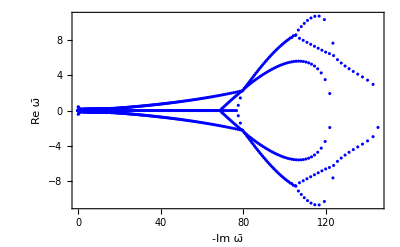

500 =n

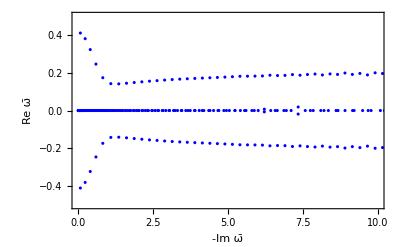

```mathematica
l500=Length[R500]-1;
d=(l500+1)/2
f500=ListPlot[
Table[{Re[R500[[k]][[2]]],Im[R500[[k]][[2]]]},{k,1,l500}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Blue]
Print[d"=n"]
h500=Show[f500,PlotRange -> {{0,10},{-1/2,1/2}},Axes->True]
```

```mathematica
R400=raices[400]
```

ω==0.00799902||ω==0.0114907||ω==0.0158313||ω==0.0247025||ω==0.025642||ω==0.0374907||ω==0.041966||ω==0.0514057||ω==0.0633707||ω==0.0674042||ω==0.0854979||ω==0.0889927||ω==0.105723||ω==0.118895||ω==0.128098||ω==0.152588||ω==0.153252||ω==0.179418||ω==0.19199||ω==0.208452||ω==0.235406||ω==0.239807||ω==0.27346||ω==0.283668||ω==0.309573||ω==0.336813||ω==0.348163||ω==0.389232||ω==0.39509||ω==0.432992||ω==0.45845||ω==0.479418||ω==0.527204||ω==0.5284||ω==0.580732||ω==0.600328||ω==0.635724||ω==0.677838||ω==0.693573||ω==0.820157||ω==0.83893||ω==0.88691||ω==0.9239||ω==0.956635||ω==1.01743||ω==1.0286||ω==1.11034||ω==1.11937||ω==1.18835||ω==1.23565||ω==1.27132||ω==1.44925||ω==1.49399||ω==1.54268||ω==1.63864||ω==1.63976||ω==1.74094||ω==1.78933||ω==1.84637||ω==1.94641||ω==1.96257||ω==2.06689||ω==2.12419||ω==2.18641||ω==2.29587||ω==2.31583||ω==2.43183||ω==2.50034||ω==2.56218||ω==2.69505||ω==2.70882||ω==2.83369||ω==2.92837||ω==2.97603||ω==3.12516||ω==3.16065||ω==3.27565||ω==3.40627||ω==3.43837||ω==3.59576||ω==3.668||ω==3.77001||ω==3.93927||ω==3.9464||ω==4.12281||ω==4.24099||ω==4.30539||ω==4.49423||ω==4.55683||ω==4.69999||ω==4.87225||ω==4.90881||ω==5.11678||ω==5.23855||ω==5.3306||ω==5.54882||ω==5.61724||ω==5.79755||ω==6.27864||ω==6.43663||ω==6.55163||ω==6.81635||ω==6.89419||ω==7.08037||ω==7.34341||ω==7.40464||ω==7.66816||ω==7.91501||ω==7.99596||ω==8.30067||ω==8.50418||ω==8.61525||ω==8.97097||ω==9.09604||ω==9.30795||ω==9.69081||ω==9.76115||ω==10.0596||ω==10.8842||ω==11.8051||ω==12.2006||ω==12.3622||ω==12.7349||ω==13.8621||ω==14.3349||ω==14.4302||ω==15.0911||ω==15.8147||ω==16.1373||ω==16.4097||ω==17.1516||ω==17.9048||ω==18.1497||ω==18.8894||ω==19.6959||ω==19.9497||ω==20.0734||ω==20.4602||ω==20.6273||ω==20.8964||ω==21.159||ω==21.4128||ω==21.6272||ω==21.9231||ω==22.1483||ω==22.3775||ω==22.7059||ω==22.8393||ω==23.1942||ω==23.375||ω==23.6439||ω==23.9351||ω==24.1002||ω==24.4571||ω==24.5948||ω==24.9319||ω==25.13||ω==25.3968||ω==25.6664||ω==25.8691||ω==26.185||ω==26.3584||ω==26.6825||ω==26.866||ω==27.1686||ω==27.3815||ω==27.6536||ω==27.8947||ω==28.1434||ω==28.4009||ω==28.6402||ω==28.9001||ω==29.143||ω==29.3948||ω==29.6488||ω==29.8882||ω==30.1546||ω==30.3827||ω==30.6583||ω==30.8797||ω==31.1593||ω==31.3792||ω==31.6579||ω==31.8809||ω==32.1549||ω==32.3839||ω==32.6509||ω==32.8879||ω==33.1461||ω==33.3924||ω==33.6411||ω==33.897||ω==34.1364||ω==34.4007||ω==34.6332||ω==34.9019||ω==35.133||ω==35.3997||ω==35.6366||ω==35.8942||ω==36.1425||ω==36.388||ω==36.6475||ω==36.8844||ω==37.1482||ω==37.3856||ω==37.6446||ω==37.8897||ω==38.1406||ω==38.3917||ω==38.6405||ω==38.8893||ω==39.1438||ω==39.3858||ω==39.6454||ω==39.8863||ω==40.142||ω==40.3906||ω==40.6379||ω==40.8923||ω==41.1385||ω==41.3894||ω==41.6414||ω==41.8877||ω==42.1402||ω==42.3907||ω==42.6366||ω==42.8924||ω==43.1371||ω==43.3895||ω==43.6398||ω==43.8885||ω==44.138||ω==44.3913||ω==44.6358||ω==44.8908||ω==45.1381||ω==45.3881||ω==45.6386||ω==45.8897||ω==46.136||ω==46.3905||ω==46.6372||ω==46.888||ω==47.1383||ω==47.3888||ω==47.636||ω==47.8898||ω==48.137||ω==48.3875||ω==48.6378||ω==48.8886||ω==49.1358||ω==49.3889||ω==49.6372||ω==49.8871||ω==50.1371||ω==50.3886||ω==50.6358||ω==50.8877||ω==51.1374||ω==51.3871||ω==51.6361||ω==51.8882||ω==52.1365||ω==52.3866||ω==52.6365||ω==52.8885||ω==53.134||ω==53.3884||ω==53.6378||ω==53.88||ω==54.1515||ω==54.3674||ω==54.6411||ω==54.971||ω==54.9977||ω==55.7825||ω==56.7411||ω==57.7308||ω==58.68||ω==59.6018||ω==60.5008||ω==61.3281||ω==0.0785661-0.410396 ⅈ||ω==0.0785661+0.410396 ⅈ||ω==0.238529-0.380674 ⅈ||ω==0.238529+0.380674 ⅈ||ω==0.408204-0.322741 ⅈ||ω==0.408204+0.322741 ⅈ||ω==0.598369-0.24593 ⅈ||ω==0.598369+0.24593 ⅈ||ω==0.756361-0.00290348 ⅈ||ω==0.756361+0.00290348 ⅈ||ω==0.826413-0.17366 ⅈ||ω==0.826413+0.17366 ⅈ||ω==1.09375-0.142375 ⅈ||ω==1.09375+0.142375 ⅈ||ω==1.35813-0.141159 ⅈ||ω==1.35813+0.141159 ⅈ||ω==1.35946-0.00468471 ⅈ||ω==1.35946+0.00468471 ⅈ||ω==1.61701-0.144514 ⅈ||ω==1.61701+0.144514 ⅈ||ω==1.87351-0.148512 ⅈ||ω==1.87351+0.148512 ⅈ||ω==2.12854-0.151867 ⅈ||ω==2.12854+0.151867 ⅈ||ω==2.38249-0.155587 ⅈ||ω==2.38249+0.155587 ⅈ||ω==2.63519-0.158588 ⅈ||ω==2.63519+0.158588 ⅈ||ω==2.88764-0.161013 ⅈ||ω==2.88764+0.161013 ⅈ||ω==3.1398-0.163294 ⅈ||ω==3.1398+0.163294 ⅈ||ω==3.39142-0.16567 ⅈ||ω==3.39142+0.16567 ⅈ||ω==3.64291-0.167891 ⅈ||ω==3.64291+0.167891 ⅈ||ω==3.89352-0.169898 ⅈ||ω==3.89352+0.169898 ⅈ||ω==4.14417-0.172689 ⅈ||ω==4.14417+0.172689 ⅈ||ω==4.39616-0.175487 ⅈ||ω==4.39616+0.175487 ⅈ||ω==4.64749-0.176134 ⅈ||ω==4.64749+0.176134 ⅈ||ω==4.89824-0.175987 ⅈ||ω==4.89824+0.175987 ⅈ||ω==5.14572-0.178635 ⅈ||ω==5.14572+0.178635 ⅈ||ω==5.39941-0.181841 ⅈ||ω==5.39941+0.181841 ⅈ||ω==5.6497-0.180982 ⅈ||ω==5.6497+0.180982 ⅈ||ω==5.89599-0.182852 ⅈ||ω==5.89599+0.182852 ⅈ||ω==6.02194-0.011346 ⅈ||ω==6.02194+0.011346 ⅈ||ω==6.15194-0.185623 ⅈ||ω==6.15194+0.185623 ⅈ||ω==6.39784-0.184566 ⅈ||ω==6.39784+0.184566 ⅈ||ω==6.64845-0.189371 ⅈ||ω==6.64845+0.189371 ⅈ||ω==6.89979-0.182001 ⅈ||ω==6.89979+0.182001 ⅈ||ω==7.15106-0.190675 ⅈ||ω==7.15106+0.190675 ⅈ||ω==7.40252-0.186737 ⅈ||ω==7.40252+0.186737 ⅈ||ω==7.64858-0.195532 ⅈ||ω==7.64858+0.195532 ⅈ||ω==7.89444-0.188577 ⅈ||ω==7.89444+0.188577 ⅈ||ω==8.14779-0.195379 ⅈ||ω==8.14779+0.195379 ⅈ||ω==8.39207-0.187362 ⅈ||ω==8.39207+0.187362 ⅈ||ω==8.65502-0.18855 ⅈ||ω==8.65502+0.18855 ⅈ||ω==8.89424-0.19131 ⅈ||ω==8.89424+0.19131 ⅈ||ω==9.1568-0.184439 ⅈ||ω==9.1568+0.184439 ⅈ||ω==9.40695-0.197055 ⅈ||ω==9.40695+0.197055 ⅈ||ω==9.64737-0.186835 ⅈ||ω==9.64737+0.186835 ⅈ||ω==9.91347-0.19195 ⅈ||ω==9.91347+0.19195 ⅈ||ω==10.1574-0.198701 ⅈ||ω==10.1574+0.198701 ⅈ||ω==10.3955-0.182422 ⅈ||ω==10.3955+0.182422 ⅈ||ω==10.4905-0.0399784 ⅈ||ω==10.4905+0.0399784 ⅈ||ω==10.6673-0.187251 ⅈ||ω==10.6673+0.187251 ⅈ||ω==10.9043-0.190882 ⅈ||ω==10.9043+0.190882 ⅈ||ω==11.1307-0.189468 ⅈ||ω==11.1307+0.189468 ⅈ||ω==11.3758-0.0611409 ⅈ||ω==11.3758+0.0611409 ⅈ||ω==11.3818-0.160444 ⅈ||ω==11.3818+0.160444 ⅈ||ω==11.6362-0.199355 ⅈ||ω==11.6362+0.199355 ⅈ||ω==11.8806-0.214343 ⅈ||ω==11.8806+0.214343 ⅈ||ω==12.129-0.216744 ⅈ||ω==12.129+0.216744 ⅈ||ω==12.4036-0.218566 ⅈ||ω==12.4036+0.218566 ⅈ||ω==12.6634-0.2247 ⅈ||ω==12.6634+0.2247 ⅈ||ω==12.9195-0.211646 ⅈ||ω==12.9195+0.211646 ⅈ||ω==13.1261-0.154146 ⅈ||ω==13.1261+0.154146 ⅈ||ω==13.2997-0.152199 ⅈ||ω==13.2997+0.152199 ⅈ||ω==13.435-0.0830881 ⅈ||ω==13.435+0.0830881 ⅈ||ω==13.6178-0.210758 ⅈ||ω==13.6178+0.210758 ⅈ||ω==13.8866-0.238534 ⅈ||ω==13.8866+0.238534 ⅈ||ω==14.1569-0.238929 ⅈ||ω==14.1569+0.238929 ⅈ||ω==14.467-0.202662 ⅈ||ω==14.467+0.202662 ⅈ||ω==14.7286-0.0888714 ⅈ||ω==14.7286+0.0888714 ⅈ||ω==14.8348-0.209085 ⅈ||ω==14.8348+0.209085 ⅈ||ω==15.1341-0.252227 ⅈ||ω==15.1341+0.252227 ⅈ||ω==15.4216-0.251895 ⅈ||ω==15.4216+0.251895 ⅈ||ω==15.6195-0.0722234 ⅈ||ω==15.6195+0.0722234 ⅈ||ω==15.7807-0.227045 ⅈ||ω==15.7807+0.227045 ⅈ||ω==16.1091-0.259154 ⅈ||ω==16.1091+0.259154 ⅈ||ω==16.4296-0.268454 ⅈ||ω==16.4296+0.268454 ⅈ||ω==16.7735-0.238016 ⅈ||ω==16.7735+0.238016 ⅈ||ω==16.7811-0.151692 ⅈ||ω==16.7811+0.151692 ⅈ||ω==17.1222-0.283284 ⅈ||ω==17.1222+0.283284 ⅈ||ω==17.4544-0.276074 ⅈ||ω==17.4544+0.276074 ⅈ||ω==17.5529-0.0831214 ⅈ||ω==17.5529+0.0831214 ⅈ||ω==17.822-0.288711 ⅈ||ω==17.822+0.288711 ⅈ||ω==18.1716-0.298562 ⅈ||ω==18.1716+0.298562 ⅈ||ω==18.5305-0.0119928 ⅈ||ω==18.5305+0.0119928 ⅈ||ω==18.5345-0.296677 ⅈ||ω==18.5345+0.296677 ⅈ||ω==18.8997-0.315178 ⅈ||ω==18.8997+0.315178 ⅈ||ω==19.2686-0.311383 ⅈ||ω==19.2686+0.311383 ⅈ||ω==19.2762-0.0937106 ⅈ||ω==19.2762+0.0937106 ⅈ||ω==19.6417-0.330012 ⅈ||ω==19.6417+0.330012 ⅈ||ω==20.0232-0.331481 ⅈ||ω==20.0232+0.331481 ⅈ||ω==20.4035-0.344119 ⅈ||ω==20.4035+0.344119 ⅈ||ω==20.7944-0.350986 ⅈ||ω==20.7944+0.350986 ⅈ||ω==21.1858-0.360316 ⅈ||ω==21.1858+0.360316 ⅈ||ω==21.5849-0.368666 ⅈ||ω==21.5849+0.368666 ⅈ||ω==21.9861-0.377679 ⅈ||ω==21.9861+0.377679 ⅈ||ω==22.3948-0.387789 ⅈ||ω==22.3948+0.387789 ⅈ||ω==22.8074-0.395827 ⅈ||ω==22.8074+0.395827 ⅈ||ω==23.2239-0.406048 ⅈ||ω==23.2239+0.406048 ⅈ||ω==23.6474-0.416577 ⅈ||ω==23.6474+0.416577 ⅈ||ω==24.0757-0.4259 ⅈ||ω==24.0757+0.4259 ⅈ||ω==24.5082-0.435969 ⅈ||ω==24.5082+0.435969 ⅈ||ω==24.9465-0.446979 ⅈ||ω==24.9465+0.446979 ⅈ||ω==25.3908-0.457864 ⅈ||ω==25.3908+0.457864 ⅈ||ω==25.8403-0.468599 ⅈ||ω==25.8403+0.468599 ⅈ||ω==26.295-0.479658 ⅈ||ω==26.295+0.479658 ⅈ||ω==26.7554-0.491176 ⅈ||ω==26.7554+0.491176 ⅈ||ω==27.2216-0.503005 ⅈ||ω==27.2216+0.503005 ⅈ||ω==27.6936-0.51504 ⅈ||ω==27.6936+0.51504 ⅈ||ω==28.1715-0.52729 ⅈ||ω==28.1715+0.52729 ⅈ||ω==28.6554-0.539806 ⅈ||ω==28.6554+0.539806 ⅈ||ω==29.1453-0.552621 ⅈ||ω==29.1453+0.552621 ⅈ||ω==29.6413-0.565747 ⅈ||ω==29.6413+0.565747 ⅈ||ω==30.1436-0.579184 ⅈ||ω==30.1436+0.579184 ⅈ||ω==30.6523-0.592938 ⅈ||ω==30.6523+0.592938 ⅈ||ω==31.1674-0.607017 ⅈ||ω==31.1674+0.607017 ⅈ||ω==31.6892-0.621434 ⅈ||ω==31.6892+0.621434 ⅈ||ω==32.2176-0.636199 ⅈ||ω==32.2176+0.636199 ⅈ||ω==32.7529-0.651325 ⅈ||ω==32.7529+0.651325 ⅈ||ω==33.2952-0.666824 ⅈ||ω==33.2952+0.666824 ⅈ||ω==33.8445-0.682706 ⅈ||ω==33.8445+0.682706 ⅈ||ω==34.4011-0.698985 ⅈ||ω==34.4011+0.698985 ⅈ||ω==34.965-0.715675 ⅈ||ω==34.965+0.715675 ⅈ||ω==35.5365-0.732792 ⅈ||ω==35.5365+0.732792 ⅈ||ω==36.1156-0.750351 ⅈ||ω==36.1156+0.750351 ⅈ||ω==36.7027-0.768366 ⅈ||ω==36.7027+0.768366 ⅈ||ω==37.2977-0.786856 ⅈ||ω==37.2977+0.786856 ⅈ||ω==37.901-0.805839 ⅈ||ω==37.901+0.805839 ⅈ||ω==38.5126-0.825332 ⅈ||ω==38.5126+0.825332 ⅈ||ω==39.1328-0.845356 ⅈ||ω==39.1328+0.845356 ⅈ||ω==39.7619-0.865932 ⅈ||ω==39.7619+0.865932 ⅈ||ω==40.4-0.887082 ⅈ||ω==40.4+0.887082 ⅈ||ω==41.0473-0.90883 ⅈ||ω==41.0473+0.90883 ⅈ||ω==41.7042-0.931202 ⅈ||ω==41.7042+0.931202 ⅈ||ω==42.3708-0.954225 ⅈ||ω==42.3708+0.954225 ⅈ||ω==43.0475-0.977926 ⅈ||ω==43.0475+0.977926 ⅈ||ω==43.7345-1.00234 ⅈ||ω==43.7345+1.00234 ⅈ||ω==44.4321-1.02749 ⅈ||ω==44.4321+1.02749 ⅈ||ω==45.1408-1.05342 ⅈ||ω==45.1408+1.05342 ⅈ||ω==45.8607-1.08016 ⅈ||ω==45.8607+1.08016 ⅈ||ω==46.5923-1.10776 ⅈ||ω==46.5923+1.10776 ⅈ||ω==47.3359-1.13626 ⅈ||ω==47.3359+1.13626 ⅈ||ω==48.0921-1.1657 ⅈ||ω==48.0921+1.1657 ⅈ||ω==48.8612-1.19614 ⅈ||ω==48.8612+1.19614 ⅈ||ω==49.6438-1.22763 ⅈ||ω==49.6438+1.22763 ⅈ||ω==50.4403-1.26023 ⅈ||ω==50.4403+1.26023 ⅈ||ω==51.2512-1.294 ⅈ||ω==51.2512+1.294 ⅈ||ω==52.0774-1.32902 ⅈ||ω==52.0774+1.32902 ⅈ||ω==52.9192-1.36536 ⅈ||ω==52.9192+1.36536 ⅈ||ω==53.7776-1.4031 ⅈ||ω==53.7776+1.4031 ⅈ||ω==54.6532-1.44235 ⅈ||ω==54.6532+1.44235 ⅈ||ω==55.5301-0.128297 ⅈ||ω==55.5301+0.128297 ⅈ||ω==55.5469-1.4832 ⅈ||ω==55.5469+1.4832 ⅈ||ω==56.2058-0.299392 ⅈ||ω==56.2058+0.299392 ⅈ||ω==56.4596-1.52576 ⅈ||ω==56.4596+1.52576 ⅈ||ω==56.8486-0.416709 ⅈ||ω==56.8486+0.416709 ⅈ||ω==57.3924-1.57017 ⅈ||ω==57.3924+1.57017 ⅈ||ω==57.4834-0.559276 ⅈ||ω==57.4834+0.559276 ⅈ||ω==58.1359-0.698323 ⅈ||ω==58.1359+0.698323 ⅈ||ω==58.3464-1.6166 ⅈ||ω==58.3464+1.6166 ⅈ||ω==58.7922-0.834545 ⅈ||ω==58.7922+0.834545 ⅈ||ω==59.3229-1.66498 ⅈ||ω==59.3229+1.66498 ⅈ||ω==59.4545-0.973426 ⅈ||ω==59.4545+0.973426 ⅈ||ω==60.1218-1.11069 ⅈ||ω==60.1218+1.11069 ⅈ||ω==60.3234-1.71659 ⅈ||ω==60.3234+1.71659 ⅈ||ω==60.8006-1.24517 ⅈ||ω==60.8006+1.24517 ⅈ||ω==61.3473-1.76724 ⅈ||ω==61.3473+1.76724 ⅈ||ω==61.4872-1.39 ⅈ||ω==61.4872+1.39 ⅈ||ω==62.1624-1.52189 ⅈ||ω==62.1624+1.52189 ⅈ||ω==62.2476-0.470878 ⅈ||ω==62.2476+0.470878 ⅈ||ω==62.4064-1.83262 ⅈ||ω==62.4064+1.83262 ⅈ||ω==62.8745-1.63979 ⅈ||ω==62.8745+1.63979 ⅈ||ω==63.2748-1.28582 ⅈ||ω==63.2748+1.28582 ⅈ||ω==63.4473-1.893 ⅈ||ω==63.4473+1.893 ⅈ||ω==63.6344-1.82829 ⅈ||ω==63.6344+1.82829 ⅈ||ω==64.1784-1.91055 ⅈ||ω==64.1784+1.91055 ⅈ||ω==64.4047-1.94284 ⅈ||ω==64.4047+1.94284 ⅈ||ω==64.7224-2.12654 ⅈ||ω==64.7224+2.12654 ⅈ||ω==65.0535-2.09937 ⅈ||ω==65.0535+2.09937 ⅈ||ω==65.4138-2.30587 ⅈ||ω==65.4138+2.30587 ⅈ||ω==65.7684-2.25652 ⅈ||ω==65.7684+2.25652 ⅈ||ω==66.0172-2.48428 ⅈ||ω==66.0172+2.48428 ⅈ||ω==66.5011-2.40238 ⅈ||ω==66.5011+2.40238 ⅈ||ω==66.6504-2.67202 ⅈ||ω==66.6504+2.67202 ⅈ||ω==67.2558-2.54498 ⅈ||ω==67.2558+2.54498 ⅈ||ω==67.2614-2.85503 ⅈ||ω==67.2614+2.85503 ⅈ||ω==67.8866-3.05268 ⅈ||ω==67.8866+3.05268 ⅈ||ω==68.0189-2.67505 ⅈ||ω==68.0189+2.67505 ⅈ||ω==68.5178-3.24604 ⅈ||ω==68.5178+3.24604 ⅈ||ω==68.7883-2.80332 ⅈ||ω==68.7883+2.80332 ⅈ||ω==69.1567-3.43813 ⅈ||ω==69.1567+3.43813 ⅈ||ω==69.5674-2.93115 ⅈ||ω==69.5674+2.93115 ⅈ||ω==69.7995-3.62652 ⅈ||ω==69.7995+3.62652 ⅈ||ω==70.3578-3.05777 ⅈ||ω==70.3578+3.05777 ⅈ||ω==70.447-3.81365 ⅈ||ω==70.447+3.81365 ⅈ||ω==71.0991-3.99888 ⅈ||ω==71.0991+3.99888 ⅈ||ω==71.1603-3.18234 ⅈ||ω==71.1603+3.18234 ⅈ||ω==71.7566-4.18261 ⅈ||ω==71.7566+4.18261 ⅈ||ω==71.9751-3.30447 ⅈ||ω==71.9751+3.30447 ⅈ||ω==72.4196-4.36413 ⅈ||ω==72.4196+4.36413 ⅈ||ω==72.8029-3.4239 ⅈ||ω==72.8029+3.4239 ⅈ||ω==73.0882-4.5434 ⅈ||ω==73.0882+4.5434 ⅈ||ω==73.6444-3.54033 ⅈ||ω==73.6444+3.54033 ⅈ||ω==73.7624-4.72011 ⅈ||ω==73.7624+4.72011 ⅈ||ω==74.4425-4.89414 ⅈ||ω==74.4425+4.89414 ⅈ||ω==74.5004-3.65336 ⅈ||ω==74.5004+3.65336 ⅈ||ω==75.1287-5.06528 ⅈ||ω==75.1287+5.06528 ⅈ||ω==75.3719-3.76251 ⅈ||ω==75.3719+3.76251 ⅈ||ω==75.8211-5.23328 ⅈ||ω==75.8211+5.23328 ⅈ||ω==76.2598-3.86723 ⅈ||ω==76.2598+3.86723 ⅈ||ω==76.52-5.39775 ⅈ||ω==76.52+5.39775 ⅈ||ω==77.1653-3.96688 ⅈ||ω==77.1653+3.96688 ⅈ||ω==77.2254-5.55868 ⅈ||ω==77.2254+5.55868 ⅈ||ω==77.9382-5.71539 ⅈ||ω==77.9382+5.71539 ⅈ||ω==78.0897-4.06073 ⅈ||ω==78.0897+4.06073 ⅈ||ω==78.6569-5.86712 ⅈ||ω==78.6569+5.86712 ⅈ||ω==79.0345-4.14787 ⅈ||ω==79.0345+4.14787 ⅈ||ω==79.3842-6.01683 ⅈ||ω==79.3842+6.01683 ⅈ||ω==80.0016-4.22722 ⅈ||ω==80.0016+4.22722 ⅈ||ω==80.1212-6.15456 ⅈ||ω==80.1212+6.15456 ⅈ||ω==80.8534-6.29562 ⅈ||ω==80.8534+6.29562 ⅈ||ω==80.9928-4.29745 ⅈ||ω==80.9928+4.29745 ⅈ||ω==81.6284-6.43148 ⅈ||ω==81.6284+6.43148 ⅈ||ω==82.0107-4.35695 ⅈ||ω==82.0107+4.35695 ⅈ||ω==82.3501-6.51657 ⅈ||ω==82.3501+6.51657 ⅈ||ω==83.0582-4.40362 ⅈ||ω==83.0582+4.40362 ⅈ||ω==83.1354-6.73597 ⅈ||ω==83.1354+6.73597 ⅈ||ω==83.9769-6.61076 ⅈ||ω==83.9769+6.61076 ⅈ||ω==84.1388-4.43486 ⅈ||ω==84.1388+4.43486 ⅈ||ω==84.5182-7.02014 ⅈ||ω==84.5182+7.02014 ⅈ||ω==85.2569-4.44712 ⅈ||ω==85.2569+4.44712 ⅈ||ω==85.8006-7.38583 ⅈ||ω==85.8006+7.38583 ⅈ||ω==85.8277-6.46888 ⅈ||ω==85.8277+6.46888 ⅈ||ω==86.4182-4.43558 ⅈ||ω==86.4182+4.43558 ⅈ||ω==87.2246-7.76957 ⅈ||ω==87.2246+7.76957 ⅈ||ω==87.6299-4.39382 ⅈ||ω==87.6299+4.39382 ⅈ||ω==87.6449-6.24146 ⅈ||ω==87.6449+6.24146 ⅈ||ω==88.7621-8.10258 ⅈ||ω==88.7621+8.10258 ⅈ||ω==88.9018-4.31152 ⅈ||ω==88.9018+4.31152 ⅈ||ω==89.4576-6.01777 ⅈ||ω==89.4576+6.01777 ⅈ||ω==90.2485-4.17305 ⅈ||ω==90.2485+4.17305 ⅈ||ω==90.451-8.36392 ⅈ||ω==90.451+8.36392 ⅈ||ω==91.2697-5.79542 ⅈ||ω==91.2697+5.79542 ⅈ||ω==91.692-3.95178 ⅈ||ω==91.692+3.95178 ⅈ||ω==92.3768-8.48886 ⅈ||ω==92.3768+8.48886 ⅈ||ω==93.0803-5.57436 ⅈ||ω==93.0803+5.57436 ⅈ||ω==93.2705-3.59705 ⅈ||ω==93.2705+3.59705 ⅈ||ω==94.693-8.3048 ⅈ||ω==94.693+8.3048 ⅈ||ω==94.8861-5.35818 ⅈ||ω==94.8861+5.35818 ⅈ||ω==95.0534-2.99338 ⅈ||ω==95.0534+2.99338 ⅈ||ω==96.6972-5.18803 ⅈ||ω==96.6972+5.18803 ⅈ||ω==97.1477-1.68778 ⅈ||ω==97.1477+1.68778 ⅈ||ω==98.3947-6.17949 ⅈ||ω==98.3947+6.17949 ⅈ||ω==98.7512-4.98247 ⅈ||ω==98.7512+4.98247 ⅈ||ω==100.616-4.50214 ⅈ||ω==100.616+4.50214 ⅈ||ω==102.44-4.13068 ⅈ||ω==102.44+4.13068 ⅈ||ω==104.338-3.80212 ⅈ||ω==104.338+3.80212 ⅈ||ω==106.344-3.49152 ⅈ||ω==106.344+3.49152 ⅈ||ω==108.488-3.18134 ⅈ||ω==108.488+3.18134 ⅈ||ω==110.803-2.84438 ⅈ||ω==110.803+2.84438 ⅈ||ω==113.339-2.4189 ⅈ||ω==113.339+2.4189 ⅈ||ω==115.76-1.59739 ⅈ||ω==115.76+1.59739 ⅈ

400

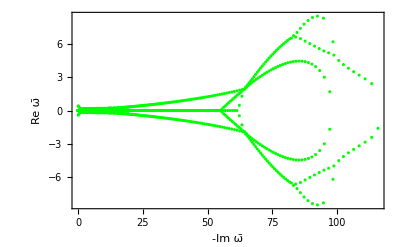

400 =n

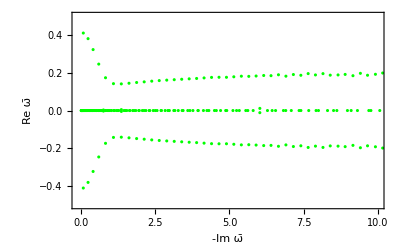

```mathematica
l400=Length[R400]-1;
d=(l400+1)/2
f400=ListPlot[
Table[{Re[R400[[k]][[2]]],Im[R400[[k]][[2]]]},{k,1,l400}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Green]
Print[d"=n"]
h400=Show[f400,PlotRange -> {{-0.1,10},{-1/2,1/2}},Axes->True]
```

%%%%    %%%%

%%%%    %%%%

```mathematica
R300=raices[300]
```

ω==0.0106592||ω==0.0153094||ω==0.0210997||ω==0.0329234||ω==0.034185||ω==0.0499976||ω==0.0559713||ω==0.0685895||ω==0.0846021||ω==0.0899959||ω==0.114242||ω==0.11898||ω==0.141412||ω==0.159247||ω==0.171548||ω==0.204601||ω==0.205765||ω==0.240997||ω==0.25844||ω==0.280516||ω==0.317818||ω==0.323406||ω==0.369572||ω==0.384275||ω==0.41944||ω==0.457679||ω==0.473048||ω==0.530198||ω==0.538547||ω==0.591795||ω==0.625461||ω==0.657491||ω==0.717145||ω==0.727525||ω==0.802289||ω==0.811237||ω==0.881252||ω==0.907133||ω==0.964696||ω==1.01177||ω==1.05285||ω==1.138||ω==1.14572||ω==1.24382||ω==1.27373||ω==1.34667||ω==1.42985||ω==1.45448||ω==1.56756||ω==1.59474||ω==1.68503||ω==1.77955||ω==1.80689||ω==1.93672||ω==1.98045||ω==2.07147||ω==2.18904||ω==2.21995||ω==2.36038||ω==2.42379||ω==2.51856||ω==2.67165||ω==2.68048||ω==2.84687||ω==2.94757||ω==3.02039||ω==3.20113||ω==3.24769||ω==3.3965||ω==3.54851||ω==3.60343||ω==3.80818||ω==3.90282||ω==4.02205||ω==4.23928||ω==4.29456||ω==4.49368||ω==4.68861||ω==4.73691||ω==4.99447||ω==5.13993||ω==5.28015||ω==5.56515||ω==5.6242||ω==5.85171||ω==6.14218||ω==6.18708||ω==6.4929||ω==6.75483||ω==6.86456||ω==7.20316||ω==7.44918||ω==7.60881||ω==7.98308||ω==8.21765||ω==8.42783||ω==8.85871||ω==9.09846||ω==9.34305||ω==9.88264||ω==10.18||ω==10.4302||ω==11.0505||ω==11.4534||ω==11.6752||ω==12.379||ω==13.1422||ω==13.3892||ω==14.0768||ω==14.9247||ω==15.7561||ω==15.8708||ω==16.137||ω==16.4347||ω==16.6554||ω==16.886||ω==17.1862||ω==17.3922||ω==17.6427||ω==17.9585||ω==18.0889||ω==18.4805||ω==18.5874||ω==18.939||ω==19.14||ω==19.3972||ω==19.678||ω==19.8721||ω==20.1867||ω==20.3722||ω==20.6747||ω==20.8872||ω==21.1595||ω==21.3993||ω==21.6519||ω==21.9006||ω==22.1551||ω==22.3921||ω==22.6661||ω==22.8792||ω==23.1782||ω==23.3682||ω==23.6843||ω==23.8646||ω==24.1804||ω==24.3714||ω==24.668||ω==24.8862||ω==25.1516||ω==25.4029||ω==25.6368||ω==25.914||ω==26.1297||ω==26.4137||ω==26.6343||ω==26.9036||ω==27.146||ω==27.3926||ω==27.6525||ω==27.8919||ω==28.1449||ω==28.4056||ω==28.6284||ω==28.9202||ω==29.1195||ω==29.4162||ω==29.6316||ω==29.8977||ω==30.1499||ω==30.387||ω==30.6488||ω==30.8971||ω==31.135||ω==31.4058||ω==31.6359||ω==31.8934||ω==32.1523||ω==32.3819||ω==32.6513||ω==32.8924||ω==33.1384||ω==33.3975||ω==33.6445||ω==33.8841||ω==34.1541||ω==34.3849||ω==34.6427||ω==34.8957||ω==35.1417||ω==35.386||ω==35.6522||ω==35.8843||ω==36.1425||ω==36.3944||ω==36.6419||ω==36.8851||ω==37.1498||ω==37.387||ω==37.6396||ω==37.8928||ω==38.1445||ω==38.3835||ω==38.6454||ω==38.8918||ω==39.1376||ω==39.39||ω==39.6433||ω==39.8899||ω==40.1394||ω==40.3813||ω==40.6726||ω==40.8485||ω==41.1483||ω==42.2571||ω==43.2115||ω==44.1645||ω==45.0776||ω==45.9327||ω==0.0785661-0.410396 ⅈ||ω==0.0785661+0.410396 ⅈ||ω==0.238529-0.380674 ⅈ||ω==0.238529+0.380674 ⅈ||ω==0.408204-0.322741 ⅈ||ω==0.408204+0.322741 ⅈ||ω==0.598369-0.24593 ⅈ||ω==0.598369+0.24593 ⅈ||ω==0.826413-0.173659 ⅈ||ω==0.826413+0.173659 ⅈ||ω==1.09372-0.142383 ⅈ||ω==1.09372+0.142383 ⅈ||ω==1.35805-0.141313 ⅈ||ω==1.35805+0.141313 ⅈ||ω==1.61727-0.14444 ⅈ||ω==1.61727+0.14444 ⅈ||ω==1.87354-0.148788 ⅈ||ω==1.87354+0.148788 ⅈ||ω==2.12807-0.152159 ⅈ||ω==2.12807+0.152159 ⅈ||ω==2.38199-0.155001 ⅈ||ω==2.38199+0.155001 ⅈ||ω==2.63486-0.157789 ⅈ||ω==2.63486+0.157789 ⅈ||ω==2.887-0.16083 ⅈ||ω==2.887+0.16083 ⅈ||ω==3.1389-0.164674 ⅈ||ω==3.1389+0.164674 ⅈ||ω==3.39182-0.167143 ⅈ||ω==3.39182+0.167143 ⅈ||ω==3.64483-0.169054 ⅈ||ω==3.64483+0.169054 ⅈ||ω==3.89425-0.168074 ⅈ||ω==3.89425+0.168074 ⅈ||ω==4.14377-0.174401 ⅈ||ω==4.14377+0.174401 ⅈ||ω==4.39725-0.175222 ⅈ||ω==4.39725+0.175222 ⅈ||ω==4.64509-0.172644 ⅈ||ω==4.64509+0.172644 ⅈ||ω==4.89805-0.181361 ⅈ||ω==4.89805+0.181361 ⅈ||ω==5.14729-0.17716 ⅈ||ω==5.14729+0.17716 ⅈ||ω==5.39584-0.183783 ⅈ||ω==5.39584+0.183783 ⅈ||ω==5.6507-0.174855 ⅈ||ω==5.6507+0.174855 ⅈ||ω==5.90084-0.185074 ⅈ||ω==5.90084+0.185074 ⅈ||ω==6.15091-0.177588 ⅈ||ω==6.15091+0.177588 ⅈ||ω==6.40307-0.191437 ⅈ||ω==6.40307+0.191437 ⅈ||ω==6.64613-0.189501 ⅈ||ω==6.64613+0.189501 ⅈ||ω==6.90623-0.19012 ⅈ||ω==6.90623+0.19012 ⅈ||ω==7.14624-0.197533 ⅈ||ω==7.14624+0.197533 ⅈ||ω==7.39509-0.191031 ⅈ||ω==7.39509+0.191031 ⅈ||ω==7.65595-0.197355 ⅈ||ω==7.65595+0.197355 ⅈ||ω==7.89571-0.203281 ⅈ||ω==7.89571+0.203281 ⅈ||ω==8.14919-0.194961 ⅈ||ω==8.14919+0.194961 ⅈ||ω==8.41271-0.198745 ⅈ||ω==8.41271+0.198745 ⅈ||ω==8.65734-0.206878 ⅈ||ω==8.65734+0.206878 ⅈ||ω==8.90428-0.186125 ⅈ||ω==8.90428+0.186125 ⅈ||ω==9.16829-0.168432 ⅈ||ω==9.16829+0.168432 ⅈ||ω==9.41572-0.177533 ⅈ||ω==9.41572+0.177533 ⅈ||ω==9.6337-0.20222 ⅈ||ω==9.6337+0.20222 ⅈ||ω==9.87352-0.208681 ⅈ||ω==9.87352+0.208681 ⅈ||ω==10.1417-0.210736 ⅈ||ω==10.1417+0.210736 ⅈ||ω==10.4223-0.214149 ⅈ||ω==10.4223+0.214149 ⅈ||ω==10.6787-0.209142 ⅈ||ω==10.6787+0.209142 ⅈ||ω==10.8774-0.182263 ⅈ||ω==10.8774+0.182263 ⅈ||ω==11.1069-0.209501 ⅈ||ω==11.1069+0.209501 ⅈ||ω==11.3818-0.22603 ⅈ||ω==11.3818+0.22603 ⅈ||ω==11.6857-0.223536 ⅈ||ω==11.6857+0.223536 ⅈ||ω==11.9563-0.193366 ⅈ||ω==11.9563+0.193366 ⅈ||ω==12.1104-0.196027 ⅈ||ω==12.1104+0.196027 ⅈ||ω==12.379-0.245367 ⅈ||ω==12.379+0.245367 ⅈ||ω==12.6747-0.238702 ⅈ||ω==12.6747+0.238702 ⅈ||ω==12.8432-0.137366 ⅈ||ω==12.8432+0.137366 ⅈ||ω==13.0666-0.236233 ⅈ||ω==13.0666+0.236233 ⅈ||ω==13.4046-0.255913 ⅈ||ω==13.4046+0.255913 ⅈ||ω==13.7469-0.239616 ⅈ||ω==13.7469+0.239616 ⅈ||ω==13.8215-0.0949481 ⅈ||ω==13.8215+0.0949481 ⅈ||ω==14.1345-0.272597 ⅈ||ω==14.1345+0.272597 ⅈ||ω==14.4733-0.258291 ⅈ||ω==14.4733+0.258291 ⅈ||ω==14.5656-0.16032 ⅈ||ω==14.5656+0.16032 ⅈ||ω==14.8725-0.289522 ⅈ||ω==14.8725+0.289522 ⅈ||ω==15.249-0.277362 ⅈ||ω==15.249+0.277362 ⅈ||ω==15.2773-0.116568 ⅈ||ω==15.2773+0.116568 ⅈ||ω==15.6365-0.304011 ⅈ||ω==15.6365+0.304011 ⅈ||ω==16.0364-0.307314 ⅈ||ω==16.0364+0.307314 ⅈ||ω==16.4333-0.319187 ⅈ||ω==16.4333+0.319187 ⅈ||ω==16.8437-0.328947 ⅈ||ω==16.8437+0.328947 ⅈ||ω==17.2557-0.338581 ⅈ||ω==17.2557+0.338581 ⅈ||ω==17.6775-0.351292 ⅈ||ω==17.6775+0.351292 ⅈ||ω==18.1066-0.360863 ⅈ||ω==18.1066+0.360863 ⅈ||ω==18.5398-0.371425 ⅈ||ω==18.5398+0.371425 ⅈ||ω==18.9812-0.384356 ⅈ||ω==18.9812+0.384356 ⅈ||ω==19.4312-0.396866 ⅈ||ω==19.4312+0.396866 ⅈ||ω==19.8881-0.408836 ⅈ||ω==19.8881+0.408836 ⅈ||ω==20.3521-0.421287 ⅈ||ω==20.3521+0.421287 ⅈ||ω==20.8236-0.434472 ⅈ||ω==20.8236+0.434472 ⅈ||ω==21.3033-0.448109 ⅈ||ω==21.3033+0.448109 ⅈ||ω==21.791-0.462036 ⅈ||ω==21.791+0.462036 ⅈ||ω==22.2869-0.476288 ⅈ||ω==22.2869+0.476288 ⅈ||ω==22.7912-0.490953 ⅈ||ω==22.7912+0.490953 ⅈ||ω==23.304-0.506094 ⅈ||ω==23.304+0.506094 ⅈ||ω==23.8255-0.521741 ⅈ||ω==23.8255+0.521741 ⅈ||ω==24.3559-0.537903 ⅈ||ω==24.3559+0.537903 ⅈ||ω==24.8956-0.554574 ⅈ||ω==24.8956+0.554574 ⅈ||ω==25.4446-0.571764 ⅈ||ω==25.4446+0.571764 ⅈ||ω==26.0033-0.58951 ⅈ||ω==26.0033+0.58951 ⅈ||ω==26.5719-0.607856 ⅈ||ω==26.5719+0.607856 ⅈ||ω==27.1508-0.626822 ⅈ||ω==27.1508+0.626822 ⅈ||ω==27.7401-0.646431 ⅈ||ω==27.7401+0.646431 ⅈ||ω==28.3402-0.66672 ⅈ||ω==28.3402+0.66672 ⅈ||ω==28.9514-0.687722 ⅈ||ω==28.9514+0.687722 ⅈ||ω==29.5741-0.70949 ⅈ||ω==29.5741+0.70949 ⅈ||ω==30.2087-0.73206 ⅈ||ω==30.2087+0.73206 ⅈ||ω==30.8556-0.755471 ⅈ||ω==30.8556+0.755471 ⅈ||ω==31.5152-0.779773 ⅈ||ω==31.5152+0.779773 ⅈ||ω==32.1879-0.805023 ⅈ||ω==32.1879+0.805023 ⅈ||ω==32.8743-0.831277 ⅈ||ω==32.8743+0.831277 ⅈ||ω==33.5749-0.858598 ⅈ||ω==33.5749+0.858598 ⅈ||ω==34.2904-0.887055 ⅈ||ω==34.2904+0.887055 ⅈ||ω==35.0212-0.916726 ⅈ||ω==35.0212+0.916726 ⅈ||ω==35.7682-0.947695 ⅈ||ω==35.7682+0.947695 ⅈ||ω==36.5322-0.980054 ⅈ||ω==36.5322+0.980054 ⅈ||ω==37.3138-1.01391 ⅈ||ω==37.3138+1.01391 ⅈ||ω==38.1141-1.04937 ⅈ||ω==38.1141+1.04937 ⅈ||ω==38.9341-1.08658 ⅈ||ω==38.9341+1.08658 ⅈ||ω==39.7748-1.12568 ⅈ||ω==39.7748+1.12568 ⅈ||ω==40.6376-1.16683 ⅈ||ω==40.6376+1.16683 ⅈ||ω==41.4771-0.0917691 ⅈ||ω==41.4771+0.0917691 ⅈ||ω==41.5239-1.21023 ⅈ||ω==41.5239+1.21023 ⅈ||ω==42.0388-0.183055 ⅈ||ω==42.0388+0.183055 ⅈ||ω==42.4352-1.25609 ⅈ||ω==42.4352+1.25609 ⅈ||ω==42.7055-0.348595 ⅈ||ω==42.7055+0.348595 ⅈ||ω==43.3566-0.472902 ⅈ||ω==43.3566+0.472902 ⅈ||ω==43.3734-1.3047 ⅈ||ω==43.3734+1.3047 ⅈ||ω==44.0044-0.609959 ⅈ||ω==44.0044+0.609959 ⅈ||ω==44.3402-1.35637 ⅈ||ω==44.3402+1.35637 ⅈ||ω==44.6697-0.748464 ⅈ||ω==44.6697+0.748464 ⅈ||ω==45.3394-1.41069 ⅈ||ω==45.3394+1.41069 ⅈ||ω==45.3402-0.887653 ⅈ||ω==45.3402+0.887653 ⅈ||ω==46.0179-1.018 ⅈ||ω==46.0179+1.018 ⅈ||ω==46.3697-1.47289 ⅈ||ω==46.3697+1.47289 ⅈ||ω==46.7216-1.15314 ⅈ||ω==46.7216+1.15314 ⅈ||ω==46.9184-0.353427 ⅈ||ω==46.9184+0.353427 ⅈ||ω==47.3974-1.31737 ⅈ||ω==47.3974+1.31737 ⅈ||ω==47.4486-1.51567 ⅈ||ω==47.4486+1.51567 ⅈ||ω==47.9669-1.14844 ⅈ||ω==47.9669+1.14844 ⅈ||ω==48.1476-1.41269 ⅈ||ω==48.1476+1.41269 ⅈ||ω==48.5102-1.6724 ⅈ||ω==48.5102+1.6724 ⅈ||ω==48.851-1.59188 ⅈ||ω==48.851+1.59188 ⅈ||ω==49.1634-1.70075 ⅈ||ω==49.1634+1.70075 ⅈ||ω==49.5893-1.75475 ⅈ||ω==49.5893+1.75475 ⅈ||ω==49.7468-1.93807 ⅈ||ω==49.7468+1.93807 ⅈ||ω==50.3325-1.91594 ⅈ||ω==50.3325+1.91594 ⅈ||ω==50.3875-2.07516 ⅈ||ω==50.3875+2.07516 ⅈ||ω==50.9783-2.29264 ⅈ||ω==50.9783+2.29264 ⅈ||ω==51.1146-2.03725 ⅈ||ω==51.1146+2.03725 ⅈ||ω==51.6216-2.48375 ⅈ||ω==51.6216+2.48375 ⅈ||ω==51.8859-2.16119 ⅈ||ω==51.8859+2.16119 ⅈ||ω==52.2607-2.67799 ⅈ||ω==52.2607+2.67799 ⅈ||ω==52.6706-2.28578 ⅈ||ω==52.6706+2.28578 ⅈ||ω==52.9125-2.86239 ⅈ||ω==52.9125+2.86239 ⅈ||ω==53.472-2.40969 ⅈ||ω==53.472+2.40969 ⅈ||ω==53.5651-3.04667 ⅈ||ω==53.5651+3.04667 ⅈ||ω==54.2267-3.22723 ⅈ||ω==54.2267+3.22723 ⅈ||ω==54.2907-2.53003 ⅈ||ω==54.2907+2.53003 ⅈ||ω==54.8943-3.40662 ⅈ||ω==54.8943+3.40662 ⅈ||ω==55.1273-2.64614 ⅈ||ω==55.1273+2.64614 ⅈ||ω==55.5707-3.58167 ⅈ||ω==55.5707+3.58167 ⅈ||ω==55.9828-2.75763 ⅈ||ω==55.9828+2.75763 ⅈ||ω==56.2548-3.75374 ⅈ||ω==56.2548+3.75374 ⅈ||ω==56.8589-2.86378 ⅈ||ω==56.8589+2.86378 ⅈ||ω==56.9472-3.92031 ⅈ||ω==56.9472+3.92031 ⅈ||ω==57.6473-4.08366 ⅈ||ω==57.6473+4.08366 ⅈ||ω==57.7577-2.96349 ⅈ||ω==57.7577+2.96349 ⅈ||ω==58.3588-4.24135 ⅈ||ω==58.3588+4.24135 ⅈ||ω==58.6812-3.05548 ⅈ||ω==58.6812+3.05548 ⅈ||ω==59.0757-4.38933 ⅈ||ω==59.0757+4.38933 ⅈ||ω==59.6322-3.13802 ⅈ||ω==59.6322+3.13802 ⅈ||ω==59.8032-4.54453 ⅈ||ω==59.8032+4.54453 ⅈ||ω==60.5594-4.66551 ⅈ||ω==60.5594+4.66551 ⅈ||ω==60.6138-3.20918 ⅈ||ω==60.6138+3.20918 ⅈ||ω==61.2606-4.80369 ⅈ||ω==61.2606+4.80369 ⅈ||ω==61.6302-3.26585 ⅈ||ω==61.6302+3.26585 ⅈ||ω==62.115-4.97589 ⅈ||ω==62.115+4.97589 ⅈ||ω==62.6864-3.30479 ⅈ||ω==62.6864+3.30479 ⅈ||ω==62.7554-4.90176 ⅈ||ω==62.7554+4.90176 ⅈ||ω==63.5682-5.3528 ⅈ||ω==63.5682+5.3528 ⅈ||ω==63.7885-3.31981 ⅈ||ω==63.7885+3.31981 ⅈ||ω==64.4772-4.7619 ⅈ||ω==64.4772+4.7619 ⅈ||ω==64.9471-3.30344 ⅈ||ω==64.9471+3.30344 ⅈ||ω==64.9488-5.6948 ⅈ||ω==64.9488+5.6948 ⅈ||ω==66.1726-3.24388 ⅈ||ω==66.1726+3.24388 ⅈ||ω==66.2934-4.54811 ⅈ||ω==66.2934+4.54811 ⅈ||ω==66.4404-6.03184 ⅈ||ω==66.4404+6.03184 ⅈ||ω==67.4849-3.11591 ⅈ||ω==67.4849+3.11591 ⅈ||ω==68.1077-4.32863 ⅈ||ω==68.1077+4.32863 ⅈ||ω==68.1421-6.25549 ⅈ||ω==68.1421+6.25549 ⅈ||ω==68.9215-2.87658 ⅈ||ω==68.9215+2.87658 ⅈ||ω==69.9178-4.11292 ⅈ||ω==69.9178+4.11292 ⅈ||ω==70.2313-6.25049 ⅈ||ω==70.2313+6.25049 ⅈ||ω==70.5527-2.43166 ⅈ||ω==70.5527+2.43166 ⅈ||ω==71.719-3.92877 ⅈ||ω==71.719+3.92877 ⅈ||ω==72.4947-1.42038 ⅈ||ω==72.4947+1.42038 ⅈ||ω==73.4671-4.71884 ⅈ||ω==73.4671+4.71884 ⅈ||ω==73.7843-3.77003 ⅈ||ω==73.7843+3.77003 ⅈ||ω==75.6498-3.26568 ⅈ||ω==75.6498+3.26568 ⅈ||ω==77.4963-2.90164 ⅈ||ω==77.4963+2.90164 ⅈ||ω==79.4603-2.57853 ⅈ||ω==79.4603+2.57853 ⅈ||ω==81.5926-2.25716 ⅈ||ω==81.5926+2.25716 ⅈ||ω==83.9513-1.88207 ⅈ||ω==83.9513+1.88207 ⅈ||ω==86.3546-1.25025 ⅈ||ω==86.3546+1.25025 ⅈ

300

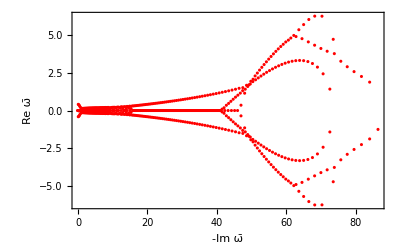

300 =n

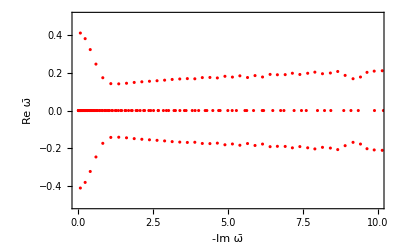

```mathematica
l300=Length[R300]-1;
d=(l300+1)/2
f300=ListPlot[
Table[{Re[R300[[k]][[2]]],Im[R300[[k]][[2]]]},{k,1,l300}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Red]
Print[d"=n"]
h300=Show[f300,PlotRange -> {{0,10},{-0.5,0.5}},Axes->True]
```

```mathematica
R200=raices[200]
```

200

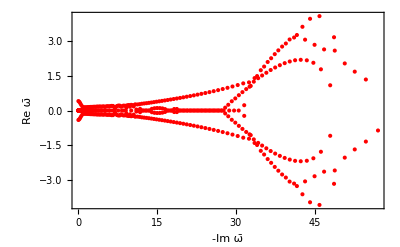

200 =n

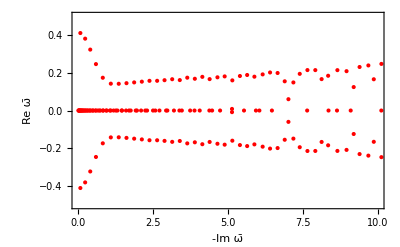

```mathematica
l200=Length[R200]-1;
d=(l200+1)/2
f200=ListPlot[
Table[{Re[R200[[k]][[2]]],Im[R200[[k]][[2]]]},{k,1,l200}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Red]
Print[d"=n"]
h200=Show[f200,PlotRange -> {{0,10},{-1/2,1/2}}, Axes->True]
```

%%%%    %%%%

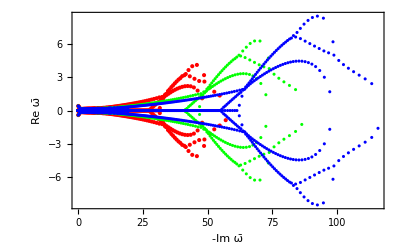

```mathematica
Show[f200,f300,f400,PlotRange -> All]
```

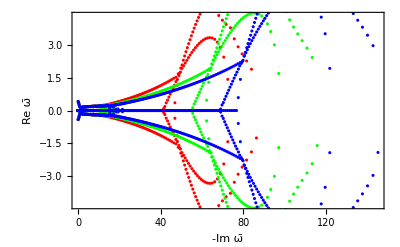

```mathematica
Show[f300,f400,f500,PlotRange -> {All,{-4.3,4.3}}]
```

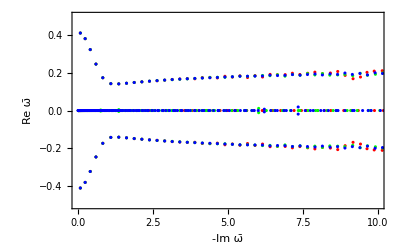

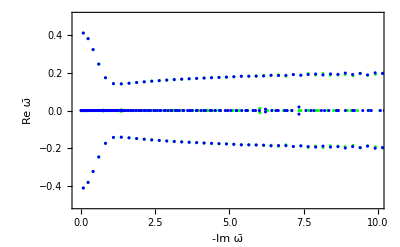

```mathematica
Show[h300,h400,h500]
Show[h400,h500]
```